# Упражнения 5-6. Някои практически въпроси, свързани с интерполацията, и приложения

#### Задача 1: Да се напише функция newtonPoly[nodes_,values_,x_], която връща в нормален вид полинома на Нютон p(x) за възлите nodes и стойности values.

```mathematica
dividedDiff[nodes_,values_]:=(
If[Length[nodes]==1,
values[[1]],
(dividedDiff[nodes[[2;;Length[nodes]]],values[[2;;Length[nodes]]]]-dividedDiff[nodes[[1;;Length[nodes]-1]],values[[1;;Length[nodes]-1]]])/(nodes[[Length[nodes]]]-nodes[[1]])]
)
newtonPoly[nodes_,values_,x_]:=(
poly=0;
product=1;
For[i=1,i≤Length[nodes],i++,
poly+=dividedDiff[nodes[[1;;i]],values[[1;;i]]]*product;
product*=x-nodes[[i]]
];
poly//Expand
)
```

#### Задача 2: В таблицата са дадени данни за населението на САЩ в периода 1920-1990. Да се построи полином от седма степен, интерполиращ таблицата. Да се даде приближение на населението през 1952, 1974, 2000 година и да се сравни с действителните стойности - съответно 157млн, 214 млн, 281.42млн. година | 1920 | 1930 | 1940 | 1950 | 1960 | 1970 | 1980 | 1990 население | 106.46 | 123.08 | 132.12 | 152.27 | 180.67 | 205.05 | 227.23 | 249.46

#### Задача 3: Да се приближи функцията f(x)=1/(1+25 x^2), като се използват полиноми от степени 10 и 4. Да се построят графиките на грешките (по абс. стойност) в двата случая

#### Задача 4: Да се състави анимация по зададените сцени:

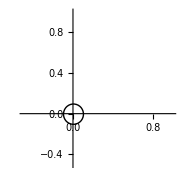
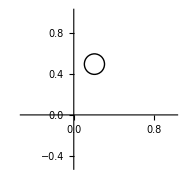
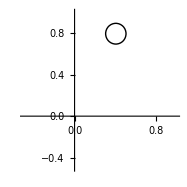

#### Задача 5 : Проведени са експерименти, за да се определи бързодействието на един алгоритъм за сортиране в зависимост от броя елементи. Резултатите са представени в следната таблица: бр. е/ти, хил | 10 | 20 | 50 | 100 | 150 | 200 | 250 време, s | 0.1639275 | 0.53282 | 3.00007 | 11.20784 | 26.7486723 | 47.3297 | 76.80605 Да се определи колко най-много елемента могат да се сортират за не повече от 30сек.